# Pi Project

In this project we will implement Ramanujan, Chudnovsky brothers, and Salamin and Brent’s methods to finding correct digits of ℼ. All methods use iteration and for each iteration the number of correct digits is increased. 
In this project we will implement those methods and find out how many right digits are added for each iteration. I will also investigate which method is faster when it come to calculating  n correct digits.

## Implementing Ramanujan’s Method

In this part we will implement Ramanujan’s method. This method is defined as bellow: 
                             -Graphics-
Now all we have to do is implement it:

```mathematica
ramanujan[n_]:=Module[{tot=0,val,k},
(* Start the loop for the sum *)
For[k=0,k≤n, k++,
(* Calculate the numerator*)
numerator=((4k)!)*(1103+26390k);
(* Calculate the denominator *)
denominator=(k!)^4 *396^(4k);
(* Find the value *)
val=numerator/denominator;
(* Add it to the total *)
tot+=val;
];
(* Multiply total by constant outside *)
tot2=(tot*2*Sqrt[2])/9801;
(* Get pi and return final *)
final=1/tot2;
Return[final]
]
```

Now let' s see if this works

```mathematica
N[ramanujan[5],50]
```

3.1415926535897932384626433832795028841971693993798

It seems to work but we need a better method to check how many values we get right. The method below will return the number of correct digits of pi that our function calculated

```mathematica
ramanujanCorrect[n_]:=Module[{steps=n},
(* Estimate pi using our function *)
piApprox2=N[ramanujan[steps],100000];
(* Get the exact value of pi *)
     piExact2=N[Pi,100000];
(* Calculate the difference *)
     piError2=Abs[piExact2-piApprox2];
(* Find the number of correct digits calculated and return *)
     Return[Floor[-Log10[piError2]]]
]
```

Now let’s try if our function works:

```mathematica
ramanujanCorrect[10]
ramanujanCorrect[20]
ramanujanCorrect[30]
```

87

167

247

It seems to work now let’s how many new steps are added each in each step. We can do this by finding the mean by diving the number of correct digits with number of steps.

```mathematica
N[ramanujanCorrect[1000]/1000,3]
```

7.99

So roughly we have 8 digits for each step. Either way I would like to see a graph of these steps. 

The way we will do this is by choosing 50 random values as the number of steps and checking if for these steps we get 8 as the number of new added digits.

```mathematica
listSteps1 ={};
For[i=2,i<50,i++,
(* Generate a random int from 2 to 1000 *)
x=RandomInteger[{2,500}];
(* Calculate the number of correct digits calculated for 1 step *)
val=ramanujanCorrect[x]-ramanujanCorrect[x-1];
(* Add that value to the list*)
AppendTo[listSteps1,val];
]
```

Now let’s plot it and see:

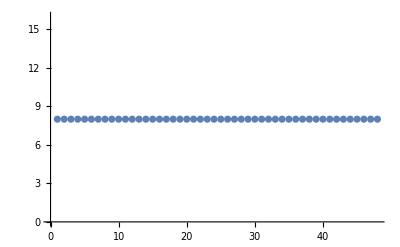

```mathematica
ListPlot[listSteps1]
```

It seems like all the steps add 8 correct digits besides some that might give only 7 steps. This explains why our average is less than 8.

## Implementing Chudnovsky Brother’s Method

In this part we will implement Chudnovsky brother’s method. This method is defined as bellow :
            -Graphics-
 It is more complicated than the previous one but the concept is the same.

```mathematica
chudnovsky[n_]:=Module[{tot=0,val,k},
(* Starting the loop for the sum *)
For[k=0,k≤n, k++,
(* Calculate numerator *)
numerator=(-1)^k*(6k)!*(13591409+545140134k);
(* Calculate denominator *)
denominator=(3k)!*(k!)^3*(640320)^(3k+3/2);
(* Find val *)
val=numerator/denominator;
(* Add to total *)
tot+=val;
];
(* Multiply by constant *)
tot2=12*tot;
(* Find pi and reverse it *)
final=1/tot2;
Return[final]
]
```

Now let’s see if this runs:

```mathematica
N[chudnovsky[2],50]
```

3.1415926535897932384626433832795028841971676788548

It seems to run just fine. Now just like above let’s write a method to calculate the right number of digits.

```mathematica
chudnovskyCorrect[n_]:=Module[{steps=n},
(* Estimate pi using our function *)
piApprox2=N[chudnovsky[steps],100000];
(* Get the exact value of pi *)
     piExact2=N[Pi,100000];
(* Calculate the difference *)
     piError2=Abs[piExact2-piApprox2];
(* Find the number of correct digits calculated and return *)
     Return[Floor[-Log10[piError2]]]
]
```

Let’s see if this works:

```mathematica
chudnovskyCorrect[10]
chudnovskyCorrect[20]
chudnovskyCorrect[30]
```

155

297

439

This seems to work as well. Just like above we will find the approximate number of steps by finding how many digits are added for each step:

```mathematica
N[chudnovskyCorrect[1000]/1000,5]
```

14.196

This is about 14.196 digits for steps. Now let’s graph it and let’s see how the number of steps look:

```mathematica
listSteps2 ={};
For[i=2,i<50,i++,
(* Generate a random int from 2 to 1000 *)
x=RandomInteger[{2,500}];
(* Calculate the number of correct digits calculated for 1 step *)
val=chudnovskyCorrect[x]-chudnovskyCorrect[x-1];
AppendTo[listSteps2,val];
]
```

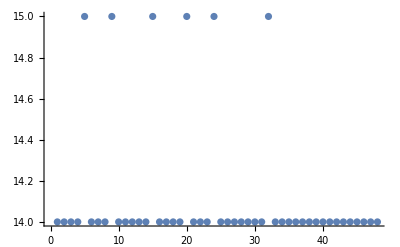

```mathematica
ListPlot[listSteps2]
```

Most values here seem to be at 14 but we have some at 15 as well. Thus the reason why we get an average number of steps of 14.196

## Implementing Salamin and Brent’s Method

In this part we will implement Salamin and Brent’s method. This method is defined as bellow :

Now all we have left to do is to implement it

```mathematica
SalaminBrent[n_]:=Module[{aPrev=1,bPrev=1/Sqrt[2],sPrev=1/2,tot},
(* Start from 1 to n *)
For[k=1,k≤n,k++,
(* Calculate the current a *)
aCurr=(aPrev+bPrev)/2;
(* Calculate the current b *)
bCurr=Sqrt[aPrev*bPrev];
(* Calculate the current c *)
cCurr=aCurr^2-bCurr^2;
(* Calculate the current s *)
sCurr=sPrev-2^k*cCurr;
(* make previous "a" to current "a" *)
aPrev=aCurr;
(* make previous "b" to current "b" *)
bPrev=bCurr;
(* make previous "s" to current "s" *)
sPrev=sCurr;
];
tot=(2 aPrev^2)/sPrev;
Return[tot]
];
```

Now let’s see if our function works:

```mathematica
N[SalaminBrent[2],50]
```

3.1416802932976532939180704245600093827957194388154

This seems to be working. Just as above let’s write a function that checks how many right digits we get:

```mathematica
SalaminBrentCorrect[n_]:=Module[{steps=n},
(* Estimate pi using our function *)
piApprox2=N[SalaminBrent[steps],100000];
(* Get the exact value of pi *)
     piExact2=N[Pi,100000];
(* Calculate the difference *)
     piError2=Abs[piExact2-piApprox2];
(* Find the number of correct digits calculated and return *)
     Return[Floor[-Log10[piError2]]]
]
```

Now let's see if this work:

```mathematica
SalaminBrentCorrect[5]
SalaminBrentCorrect[10]
SalaminBrentCorrect[13]
```

42

1395

11175

Well this seem add many more steps as the number of steps increases. Now let’s see the average for the first 13 steps:

```mathematica
N[SalaminBrentCorrect[13]/13,10]
```

859.6153846

The average seems to be 859 digits per step for the first 13 iterations but let’s graph it and see how that looks.

```mathematica
listSteps3 ={};
For[i=2,i<13,i++,
val=SalaminBrentCorrect[i]-SalaminBrentCorrect[i-1];
AppendTo[listSteps3,val];
]
```

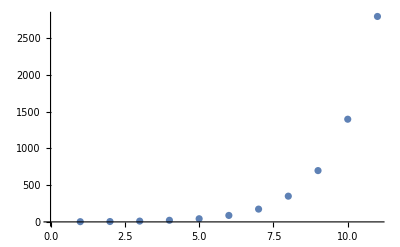

```mathematica
ListPlot[listSteps3]
```

The number of digits added  for iteration has an exponential growth so the best way to get an estimate of how many digits will we add for a certain step we would fit a line in this graph and make 
a prediction.

```mathematica
exponential=Fit[listSteps3,Exp[x1],x1]
```

0.0494578 ⅇ^x1

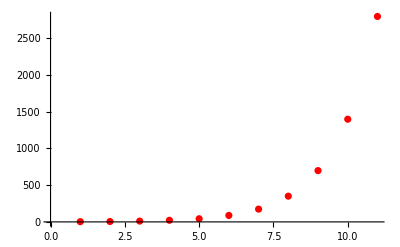

```mathematica
Show[ListPlot[listSteps3,PlotStyle->Red],Plot[parabola,{x,0,13}]]
```

So if you want to predict the number of digits for step just use the the function above and plug in the number of iterations instead of x1. The output will roughly be the number of correct digits

## Graphing the digits per step for each algorithm

Let’s also see how these steps compare to each other:

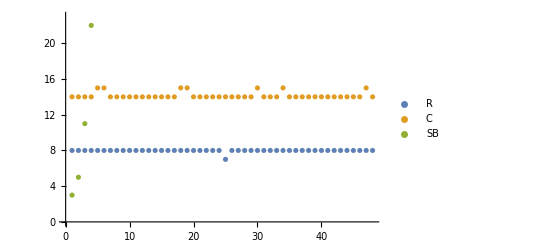

```mathematica
ListPlot[{listSteps1,listSteps2,listSteps3},PlotLegends->{"R","C","SB"}]
```

Here the steps for Salamin and Brent algorithm don’t show since they go to the hundreds and thousands. So here we only see 4 iterations of our algorithm.

## Investigating speeds - Extra

I would also like to learn which algorithm is faster when it comes to calculating large numbers of correct digits.

```mathematica
SalaminBrentCorrect[13]
```

11175

Since the Salamin and Brent method for 13 steps gives use 11175 correct digits let’s try and see how those three algorithms time against each other when trying to produce 11175 correct digits. 

For Ramanujan we divide 11175 by 8 and we will get roughly the number of required steps:

```mathematica
RamanujanSteps =Floor[N[ 11175/8]]
```

1396

Now let’s make sure we get roughly 11175 correct digits for this number of steps for the Ramanujan method.

```mathematica
ramanujanCorrect[RamanujanSteps]
```

11152

This is very close! Let’s do the same thing for the Chudnovsky brothers’ method. Now we divide by 14.2 to get the number of steps:

```mathematica
chubSteps =Floor[N[ 11175/14.2]];
chudnovskyCorrect[chubSteps]
```

11161

This also seems to be close to the number of correct digits. Now let’s time the three algorithms and see which one is faster.

```mathematica
Timing[ramanujan[RamanujanSteps]][[1]]
Timing[chudnovsky[chubSteps]][[1]]
Timing[SalaminBrent[13]][[1]]
```

1.3115

0.984592

0.018228

As we see from this example Ramanujan method is the slowest, Chudnovsky’s is the second fastest, and Salamin and Brent’s is the fastest when it comes to calculating the same number of correct digits. 

Salamin and Brent method is about 100 times faster than the Ramunjan method, and about 50 times faster than the Chudnovsky method when calculating the same number of correct digits.